#### Preamble

```mathematica
(*ClearAll["Global`*"]*)
ClearAll@@{$Context<>"*"}
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],10*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
$HistoryLength=5;
```

ScheduledTaskObject[…]

```mathematica
(*Establece el directorio de trabajo como el del cuaderno actual*)SetDirectory[NotebookDirectory[]];

(*Crea un directorio para guardar archivos relacionados con la función dieléctrica*)
CreateDirectory[dir="51.- DielectricFunction"];

(*Carga el paquete MaTeX para trabajar con ecuaciones y gráficos en LaTeX*)
<<"MaTeX`"

(*Define el tamaño de fuente a 9 puntos*)
fs=9;

(*Establece el estilo de texto para los gráficos:fuente,tamaño de letra y color negro*)
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};

(*Define las opciones de gráficos,incluyendo malla,estilo de texto,marcos,tamaño y color*)
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->ColorData[3]};

(*Aplica las opciones anteriores a todas las gráficas generadas con ListLinePlot*)
SetOptions[ListLinePlot,graphsOpts];
```

The specified WorkingDirectory is not a valid directory.  Please update the configuration ConfigureMaTeX["WorkingDirectory" -> …].

Click here for documentation on configuring MaTeX.

## Data of materials

```mathematica
h = 4.135668*^-15 (*eV s*);c = 3*^17 (*nm s^-1*);hc = h*c;
SetDirectory["C:\\Users\\ameat\\OneDrive\\Música\\Documentos\\Calculos Mie\\Respuesta de los materiales"];
materialdata=FileNames["gold.dat"];
```

The visible range is from 400nm to 780nm  (Handbook of Spectroscopy.Edited by Günter Gauglitz and Tuan Vo-Dinh, Copyright c 2003 WILEY-VCH Verlag GmbH& Co.KGaA,Weinheim, ISBN 3-527-29782-0)
that is in eV

#### Au: Johnson, P. B.; Christy, R. W. (1972). “Optical Constants of the Noble Metals”. Physical Review B. 6 (12): 4370–4379

```mathematica
(*Importa datos del archivo correspondiente a los valores de oro (Au)*)nAueV=Import[materialdata[[1]],"Data"];

(*Elimina las últimas 4 filas y las primeras 2 filas de los datos*)
nAueV=Drop[Drop[nAueV,-4],2];

(*Interpola los datos para obtener n+i*kappa en función de la energía (E=hc/lambda)*)
nAuFunc=Interpolation[nAueV/. {λ_,n_,κ_}->{hc/λ,n+I κ}];

(*Interpola los datos para obtener la permitividad dieléctrica epsilon=(n+i*kappa)^2 en función de la energía*)
εAuFunc=Interpolation[nAueV/. {λ_,n_,κ_}->{hc/λ,(n+I κ)^2}];

(*Interpolaciones separadas para las partes reales e imaginarias de epsilon*)
dummy3=Interpolation[nAueV/. {λ_,n_,κ_}->{hc/λ,n^2-κ^2},Method->"Spline"];
dummy4=Interpolation[nAueV/. {λ_,n_,κ_}->{hc/λ,2*n*κ},Method->"Spline"];

(*Función que devuelve la permitividad dieléctrica compleja interpolada*)
εAuFuncSpline[x_]:=dummy3[x]+I*dummy4[x];

(*Función para calcular el índice de refracción de nanopartículas de tamaño'a' incluyendo correcciones de tamaño*)
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ+I/γ))+(1-λ/λp^2*1/(1/λ+I (1/γ+1/γsize)))/. {λp->142.609,γ->14966.2,γsize->(a*2 π c)/(1.4*^15)}];
```

## Functions and Models

```mathematica
toMap::usage  = "Converts a non-list entry to a list so Map can be used.";
toMap = If[Length[#]==0,{#},#]&
```

If[Length[#1]==0,{#1},#1]&

```mathematica
DrudeEpsilon[w_,wp_,gamma_]:= 1 - wp^2/(w*(w+ I *gamma))
```

## Drude contribution to Gold

```mathematica
(* nAueV -> [[ev, ReEps, ImEps]]*)
epsAu  = nAueV/.{x_,y_,z_}-> {x, y^2-z^2, 2*z*y};
xx = 1 - epsAu[[;;,2]]; (*1-Re[eps]*)
omega = epsAu[[;;,1]];

y1 = omega*epsAu[[;;,3]]; (*ω*Re[eps] = γ x*)
y2 = y1^2+(omega*xx)^2 (*ω^2(Im[eps] + (1-Re[eps])) = Subscript[ω, p]^2 x*);

SetOptions[ListLogLogPlot,graphsOpts];
```

```mathematica
Table[
fit1 = NonlinearModelFit[ Take[Transpose[{xx,y1}],i], gamma*x,{gamma},x];
fit2 = NonlinearModelFit[ Take[Transpose[{xx,y2}],i], wp^2*x,{wp},x];
Prepend[#["RSquared"]&/@{fit1,fit2},i]
,{i,10,25}
];

Sort[%[[;;,{1,2}]],#1[[2]]<#2[[2]]&]
Sort[%%[[;;,{1,3}]],#1[[2]]<#2[[2]]&]
```

{{25,0.173844},{24,0.194354},{23,0.219876},{22,0.251079},{21,0.290628},{20,0.343573},{19,0.414634},{18,0.512469},{17,0.633962},{16,0.778495},{15,0.891258},{14,0.94403},{13,0.97543},{12,0.98999},{11,0.996252},{10,0.997296}}

{{25,0.994478},{24,0.994687},{23,0.994868},{22,0.995005},{21,0.99511},{20,0.995194},{19,0.995251},{18,0.995285},{16,0.995293},{17,0.995293},{15,0.995312},{14,0.995405},{13,0.995561},{12,0.995776},{11,0.996028},{10,0.996313}}

{{190.042,0.64},{91.4265,0.89},{52.0496,1.14},{33.0407,1.39},{21.6102,1.64},{14.6482,1.88},{9.11267,2.13},{4.94616,2.38},{2.70216,3.},{1.89126,4.98},{0.861829,6.1}}

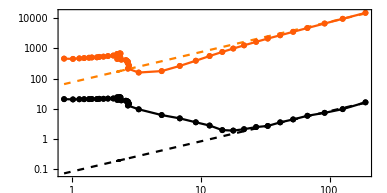

51.- DielectricFunction\DrudeFit.pdf

| Estimate | Standard Error | t-Statistic | P-Value
gamma | 0.0829512 | 0.00143964 | 57.6193 | 7.19365×10^-13

| Estimate | Standard Error | t-Statistic | P-Value
wp | 8.70461 | 0.0882527 | 98.6327 | 5.74167×10^-15

```mathematica
ii =10;
fit1 = NonlinearModelFit[ Take[Transpose[{xx,y1}],ii], gamma*x,{gamma},x];
fit2 = NonlinearModelFit[ Take[Transpose[{xx,y2}],ii], wp^2*x,{wp},x];
yy1 = fit1[x]/.x->xx;
yy2 = fit2[x]/.x->xx;

ev1 = Join@@ (Take[Transpose[{xx,omega}],#]&/@{{1,15,2},{20},{-10},{-1}})

aa = ListLogLogPlot[Transpose[{xx,#}] &/@{y1,y2},Joined->True];
bb = ListLogLogPlot[Transpose[{xx,#}] &/@{yy1,yy2},Joined->True,Mesh->None,PlotStyle->(Directive[Dashed,#,PointSize[Medium]]&/@{Black,Orange}),FrameTicks->{{Automatic,Automatic},{Automatic,ev1}}];

Show[{bb,aa},PlotRange->All,ImageSize-> 215*1.8,AspectRatio-> 1/2]
Export[FileNameJoin[{dir,"DrudeFit.pdf"}],%]

fit1["ParameterTable"]
fit2["ParameterTable"]
```

## Size correction

```mathematica
SetOptions[ListLogPlot,graphsOpts];
hcTicksInt[interval_,noLabels_,divisions_,takeLabels_]:=Module[{withLabels,smallTicks,hc},
hc = (4.13567*^-15)*(3*^17);
smallTicks={hc/#,Null}&/@FindDivisions[hc/{interval[[2]],interval[[1]]},divisions*noLabels];
withLabels ={hc/#,ToString[IntegerPart@N@#],{.02,0}}&/@FindDivisions[hc/{interval[[2]],interval[[1]]},noLabels];
withLabels=Flatten@@{Take[withLabels,{#}]&/@takeLabels,1};
Join[withLabels,smallTicks]
]
```

```mathematica
lda = (nAueV/.{x_,_,_} -> hc/x);
eV  = nAueV[[;;,1]];

jC = Transpose@ReIm[nAuFunc[lda]^2];
s1 = Transpose@ReIm[nAuSize[lda,1]^2];
s5 = Transpose@ReIm[nAuSize[lda,5]^2];
s10 = Transpose@ReIm[nAuSize[lda,10]^2];
s50 = Transpose@ReIm[nAuSize[lda,50]^2];
```

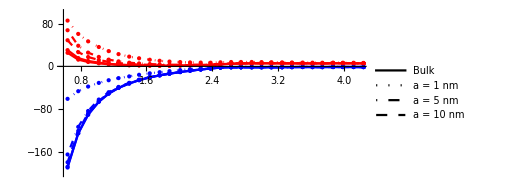

51.- DielectricFunction\JC.pdf

```mathematica
ListPlot[Transpose[{eV,#}]&/@Join[jC,s1,s5,s10,s50],Joined->True,Mesh->All,PlotRange->{{.59,4.2},{-200,100}},
PlotStyle->{Directive[Blue,PointSize[Medium]],Directive[Red,PointSize[Medium]],Directive[Blue,Dotted,PointSize[Medium]],Directive[Red,Dotted,PointSize[Medium]],
Directive[Blue,DotDashed,PointSize[Medium]],Directive[Red,DotDashed,PointSize[Medium]],Directive[Blue,Dashed,PointSize[Medium]],Directive[Red,Dashed,PointSize[Medium]]},
ImageSize-> 215*1.8,AspectRatio-> 1/2,FrameTicks->{{Automatic,Automatic},{Automatic,hcTicksInt[{1,6},20,10,{2,3,4,5,6,7,8,9,10,11}]}},
PlotLegends->Placed[
LineLegend[{Black,Directive[Dotted],Directive[DotDashed],Directive[Dashed]},#,LegendMarkerSize->15]&[
Style[#,texStyle]&/@{"Bulk","a = 1 nm","a = 5 nm","a = 10 nm","a = 50 nm"}],{Right,Top}]
]
Export[FileNameJoin[{dir,"JC.pdf"}],%]
```

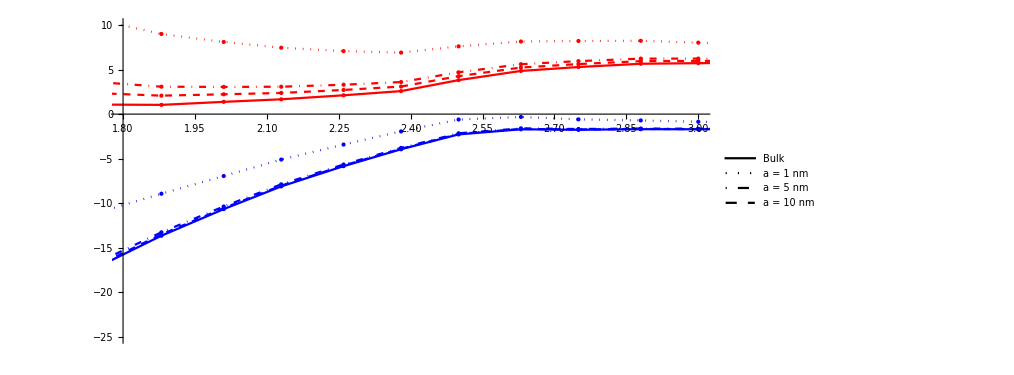

51.- DielectricFunction\JC_zoom.pdf

```mathematica
ListPlot[Transpose[{eV,#}]&/@Join[jC,s1,s5,s10],Joined->True,Mesh->All,PlotRange->{{1.8,3},{-25,10}},PlotStyle->{Directive[Blue,PointSize[Medium]],Directive[Red,PointSize[Medium]],Directive[Blue,Dotted,PointSize[Medium]],Directive[Red,Dotted,PointSize[Medium]],Directive[Blue,DotDashed,PointSize[Medium]],Directive[Red,DotDashed,PointSize[Medium]],Directive[Blue,Dashed,PointSize[Medium]],Directive[Red,Dashed,PointSize[Medium]]},ImageSize->215*1.8,AspectRatio->1/2,FrameTicks->{{{-25,-20,-15,-10,-5,0,5,10},Automatic},(*Y-axis ticks*){{1.8,2,2.2,2.4,2.6,2.8,3},Automatic} (*X-axis ticks*)},PlotLegends->Placed[LineLegend[{Black,Directive[Dotted],Directive[DotDashed],Directive[Dashed]},#,LegendMarkerSize->15]&[Style[#,texStyle]&/@{"Bulk","a = 1 nm","a = 5 nm","a = 10 nm","a = 50 nm"}],{Right,Top}]]
Export[FileNameJoin[{dir,"JC_zoom.pdf"}],%]
```